```mathematica
mypic=Import["/Users/chuanyin/Desktop/Chuan/Jan23/24.bmp"]
```

-Graphics-

rotated picture!

```mathematica
myrotpic=ImageRotate[mypic,-0.05]
ImageTake[myrotpic,{600,710},{190,-50}]
MyPic=ImageData[mypic];
```

-Graphics-

-Graphics-

278

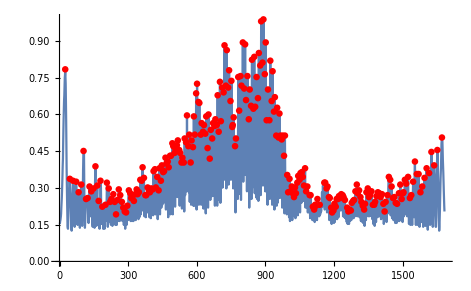

266

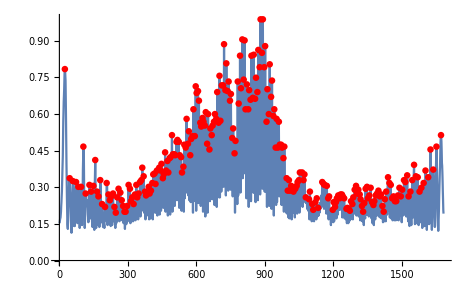

276

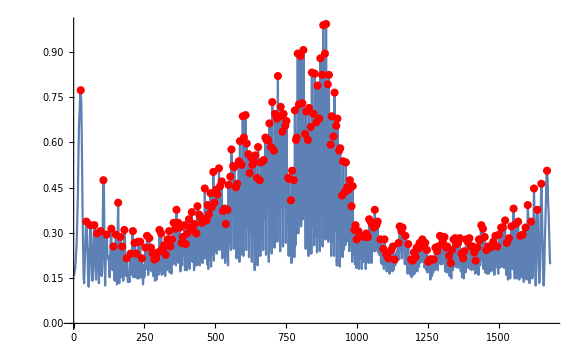

267

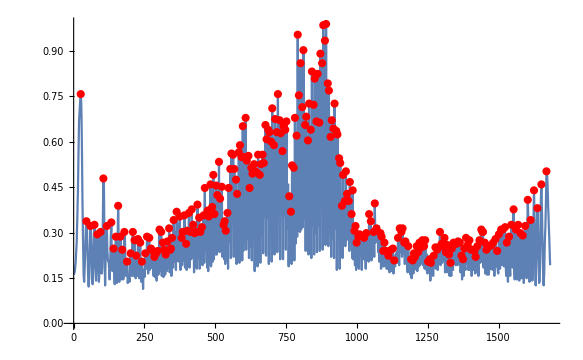

269

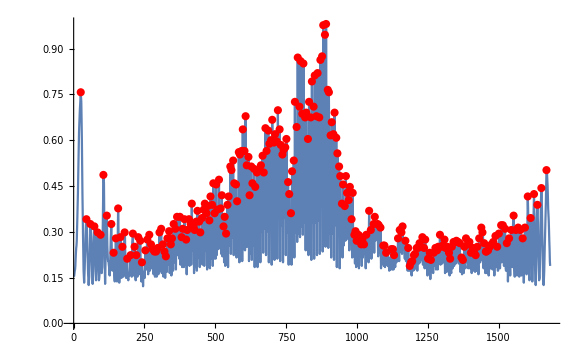

267

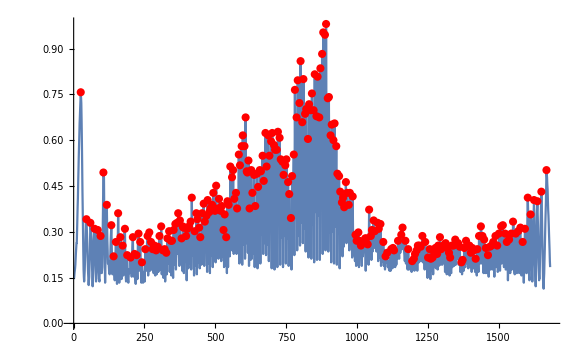

268

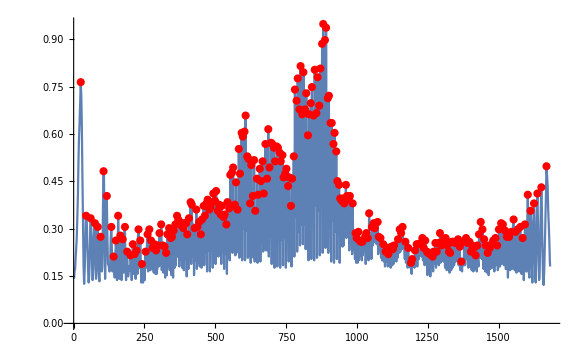

270

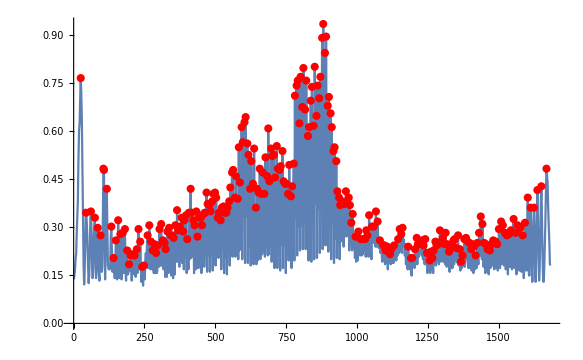

267

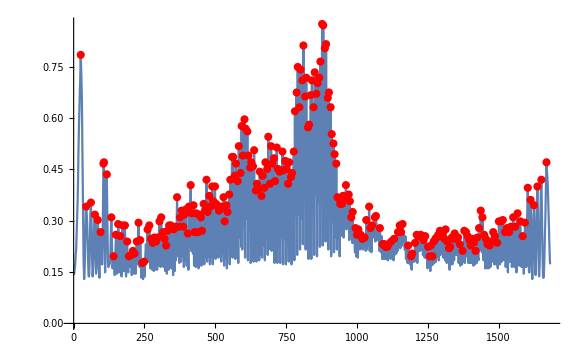

266

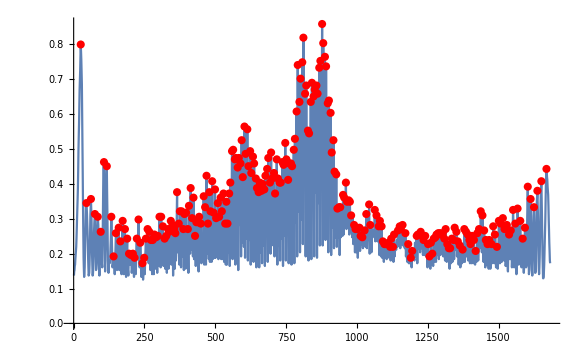

264

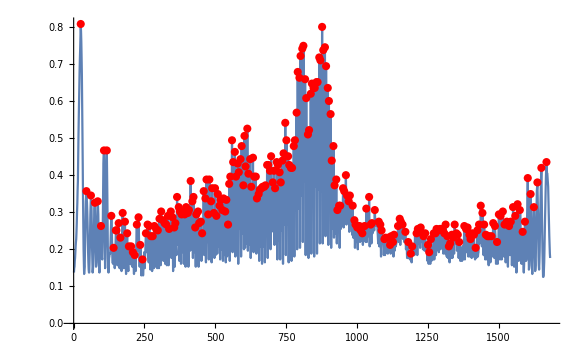

250

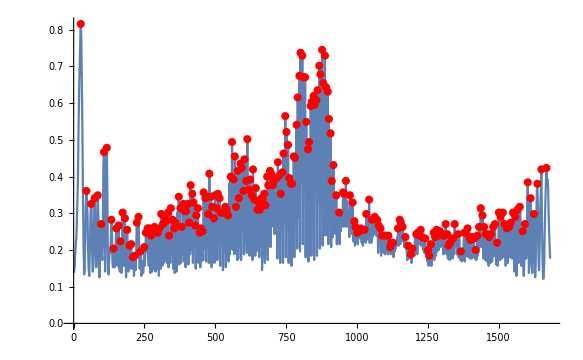

252

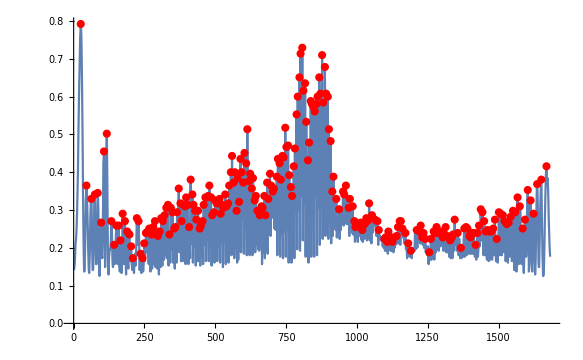

250

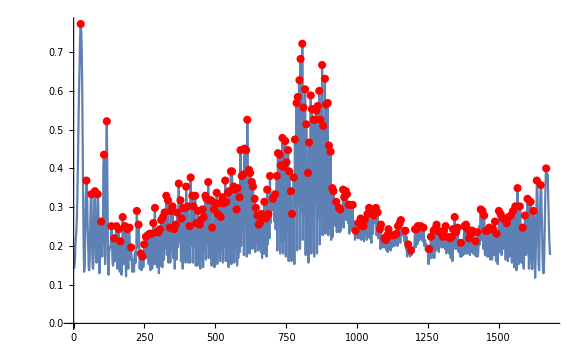

249

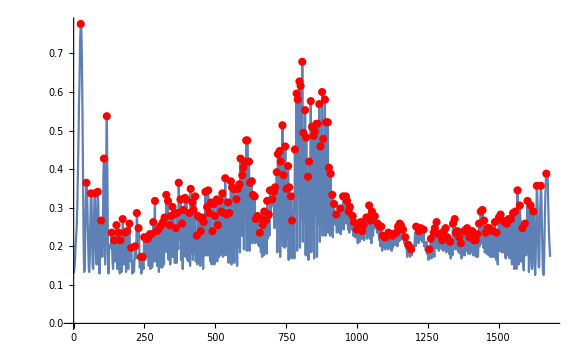

246

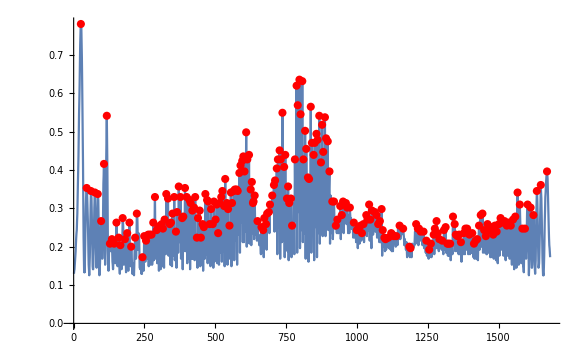

249

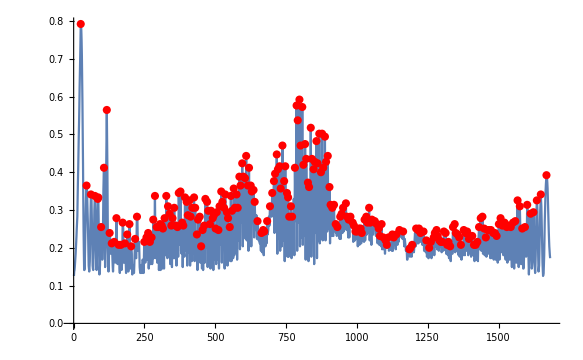

244

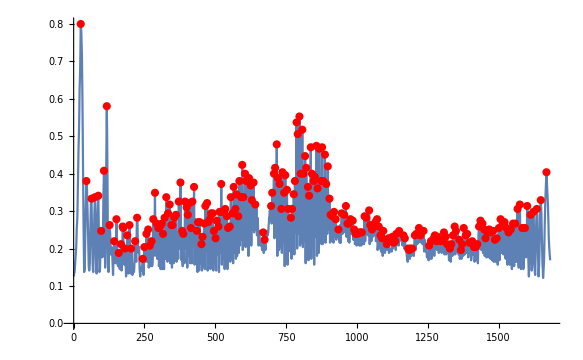

248

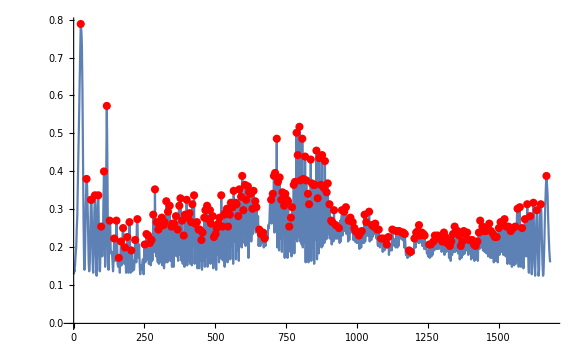

239

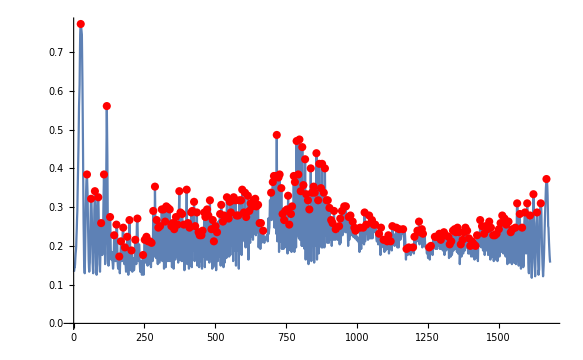

245

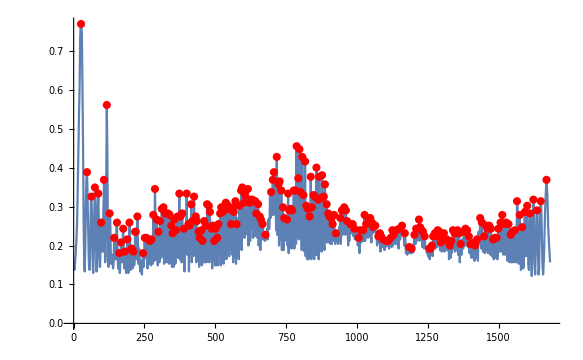

240

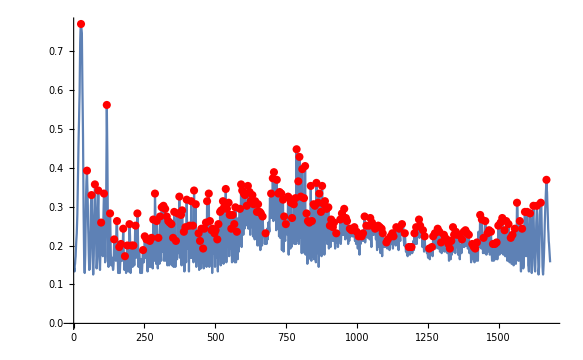

244

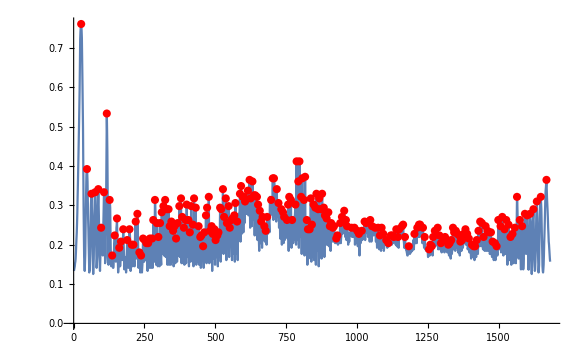

237

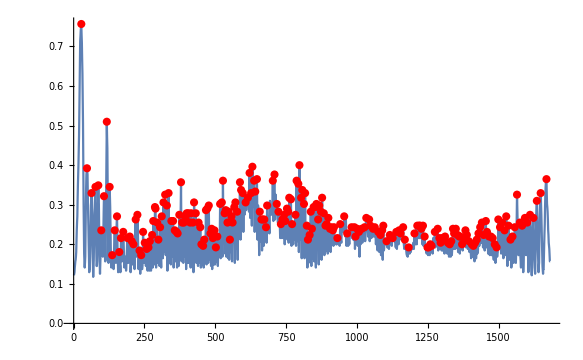

234

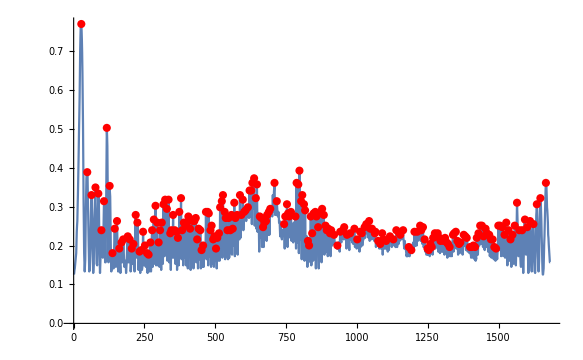

230

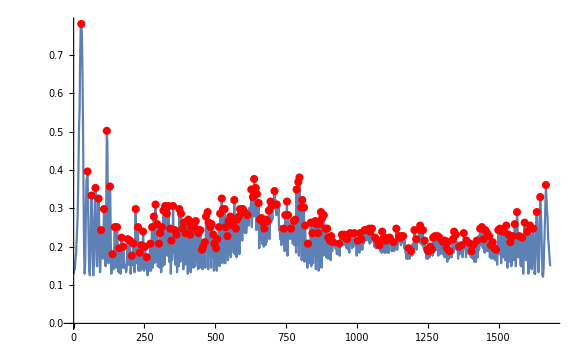

230

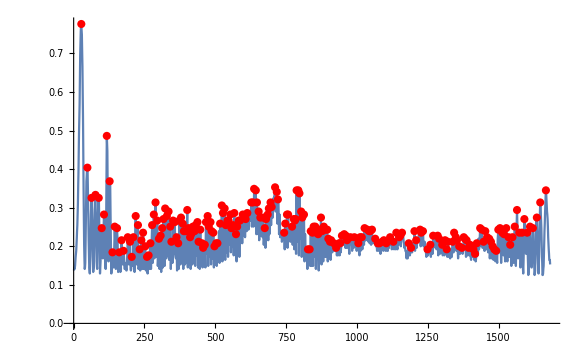

227

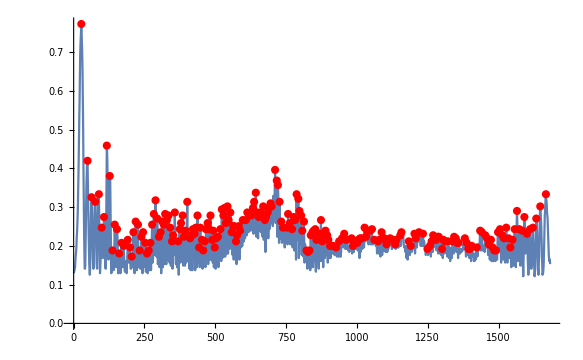

232

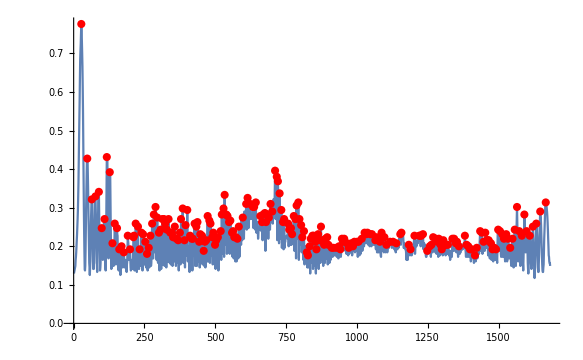

217

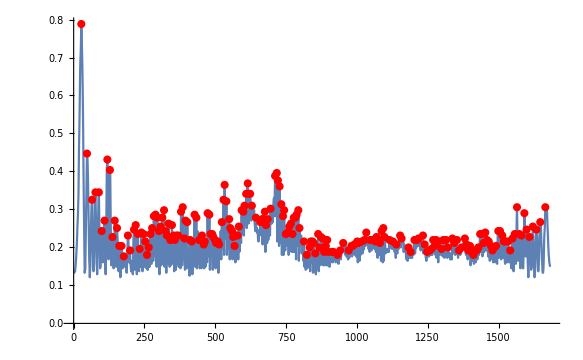

217

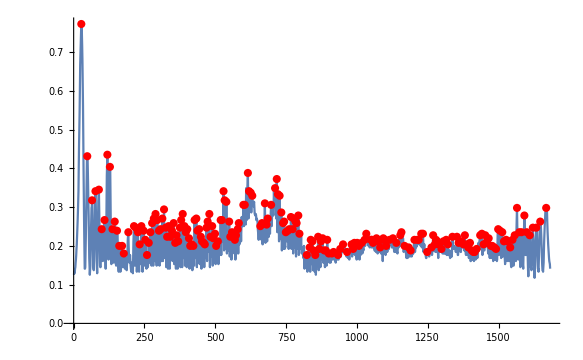

213

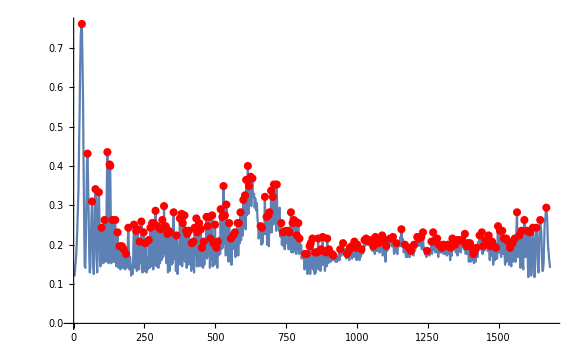

213

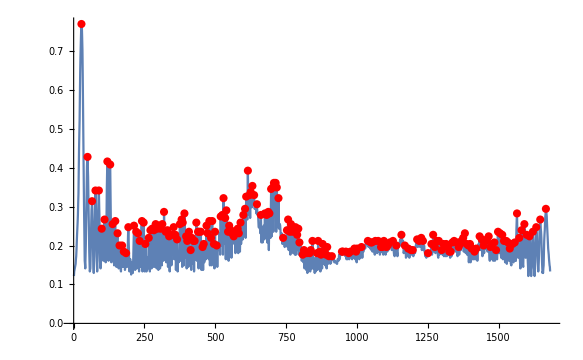

216

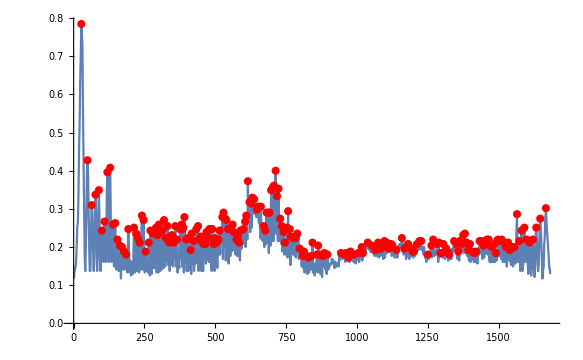

219

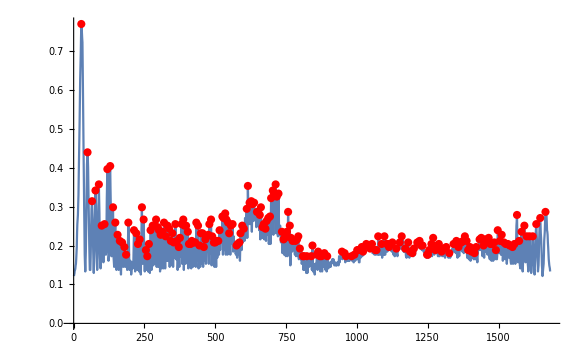

202

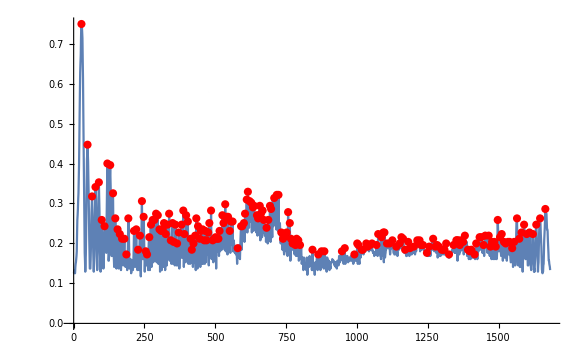

193

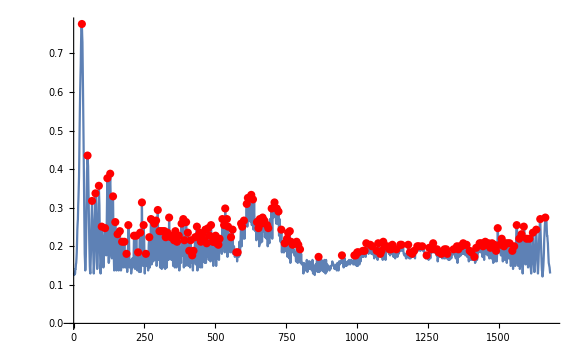

197

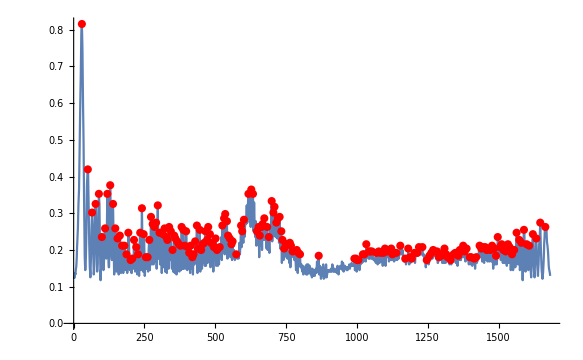

189

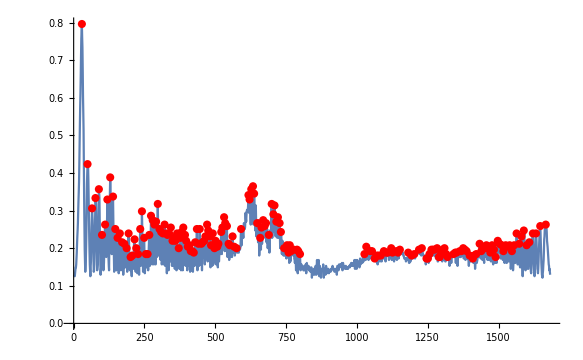

184

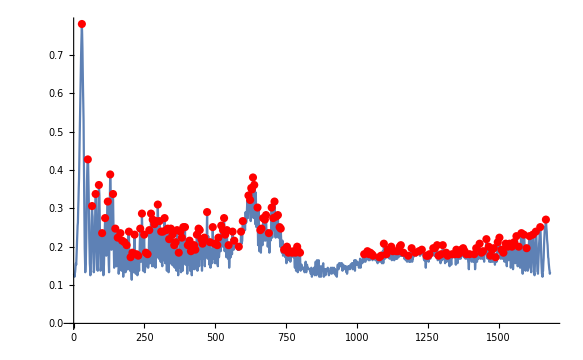

187

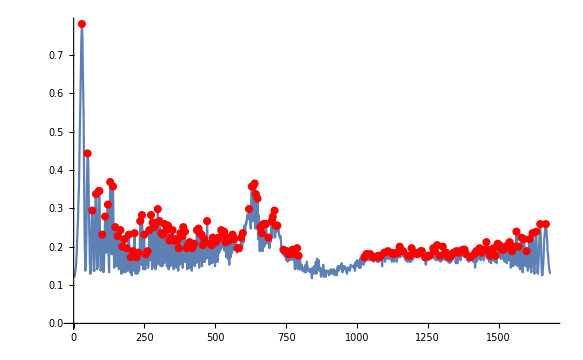

185

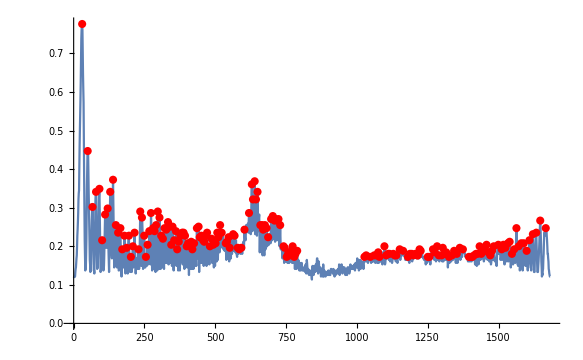

181

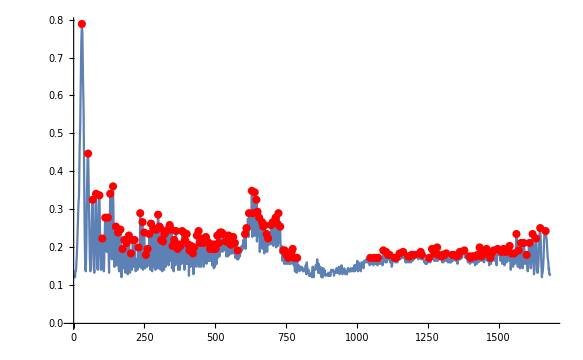

171

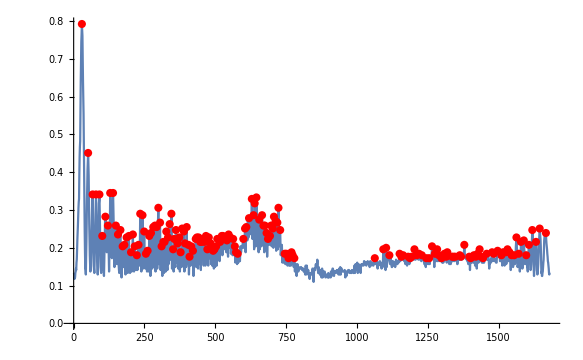

163

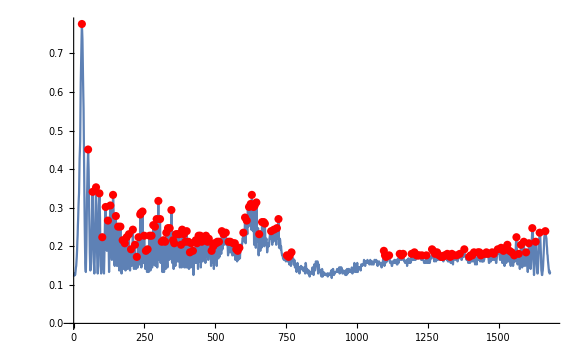

156

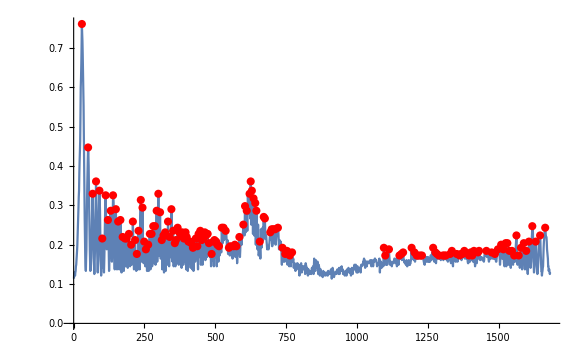

141

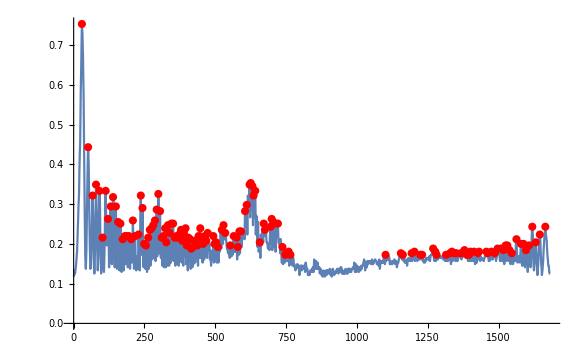

142

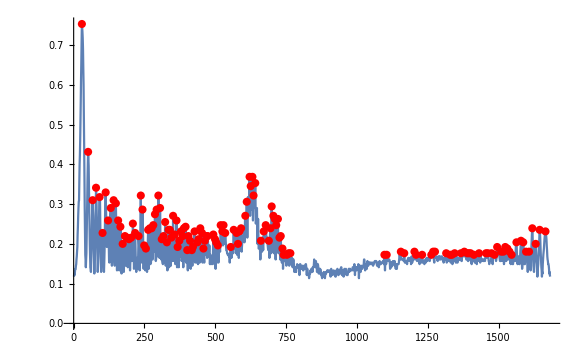

129

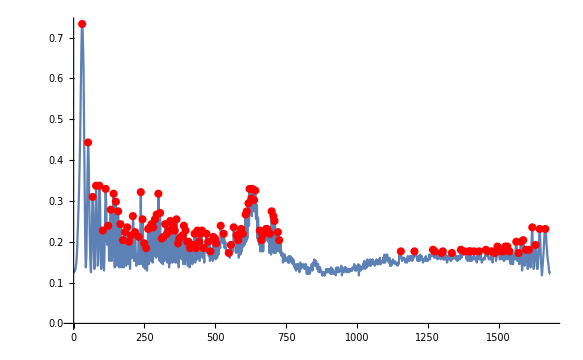

134

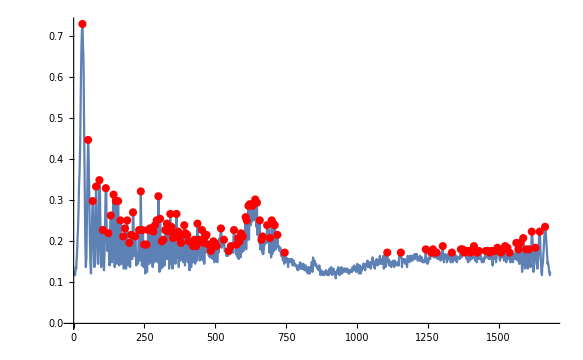

121

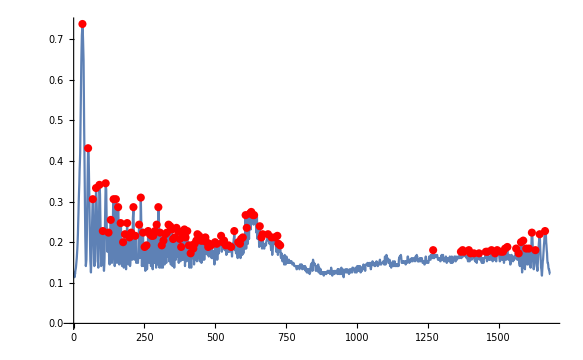

117

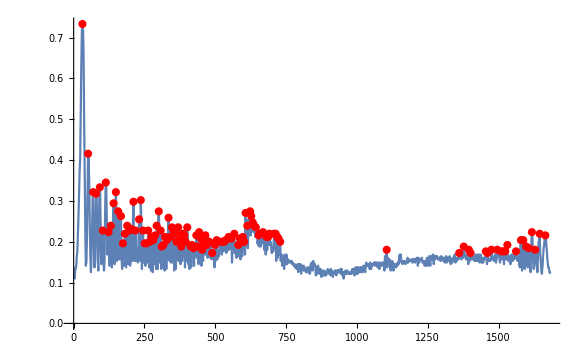

117

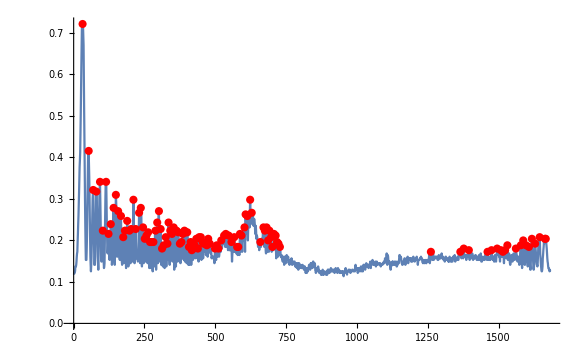

110

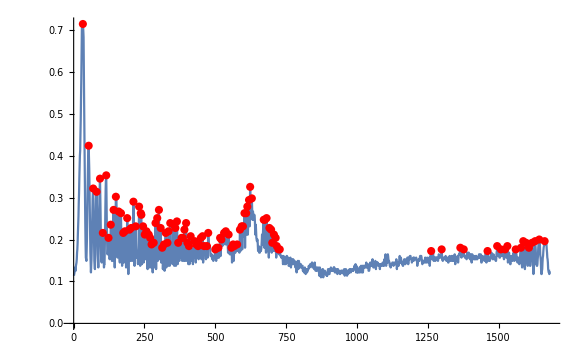

104

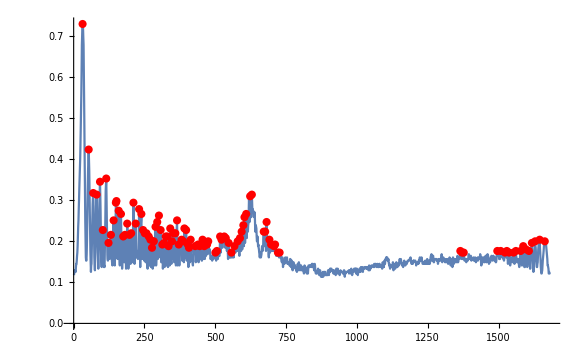

98

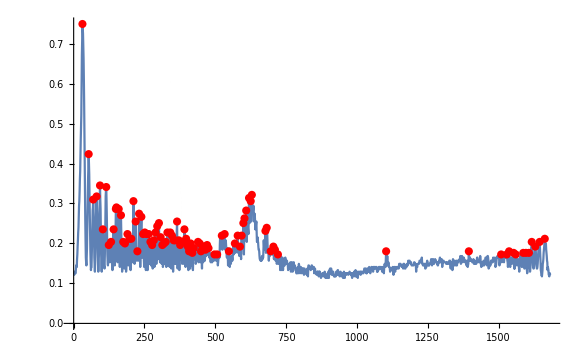

96

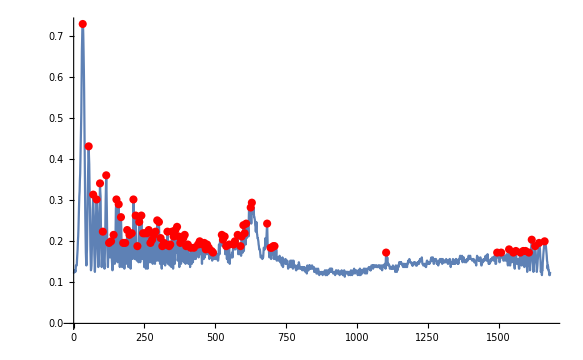

97

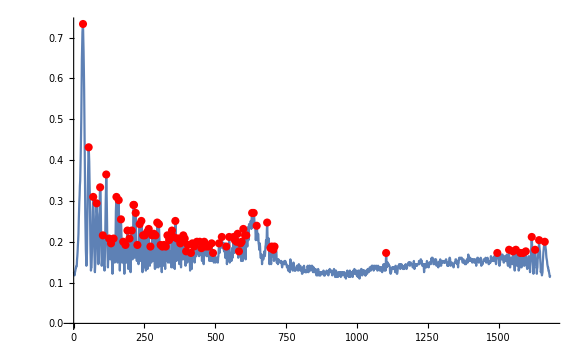

102

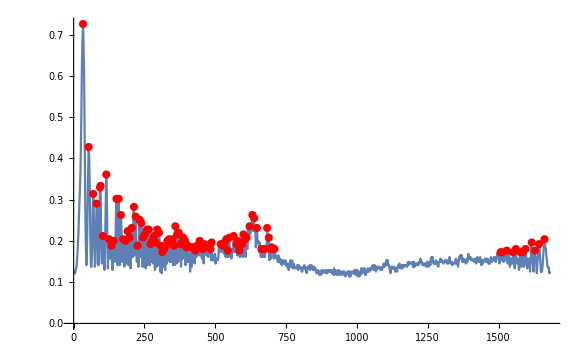

96

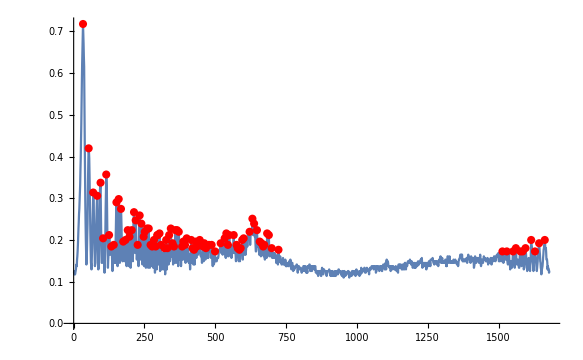

87

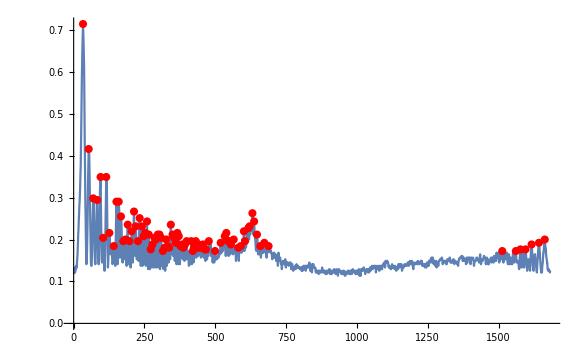

90

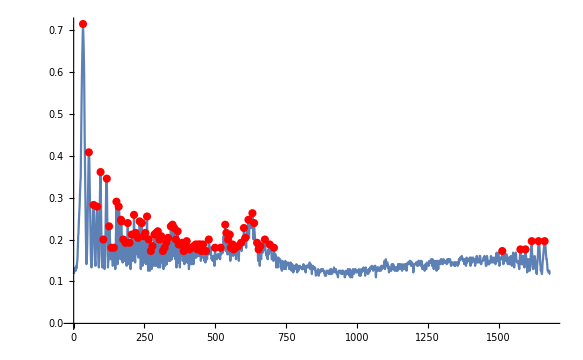

82

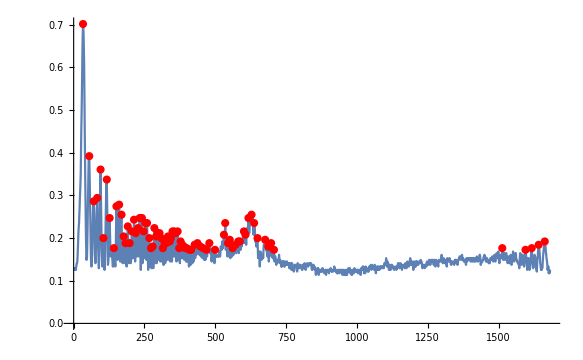

72

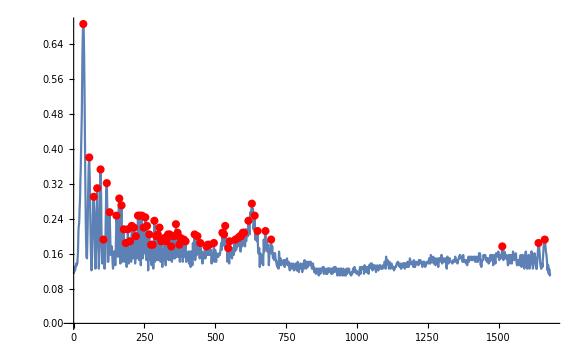

73

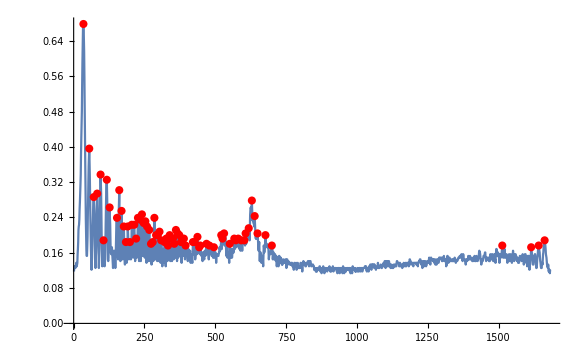

72

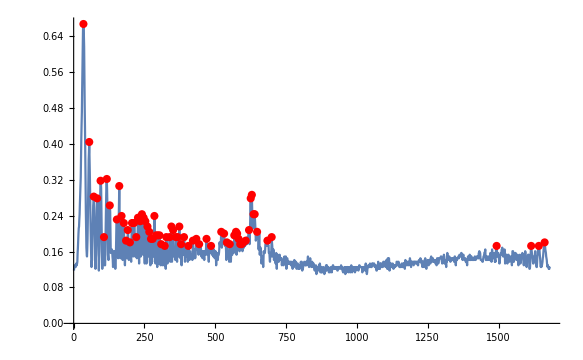

66

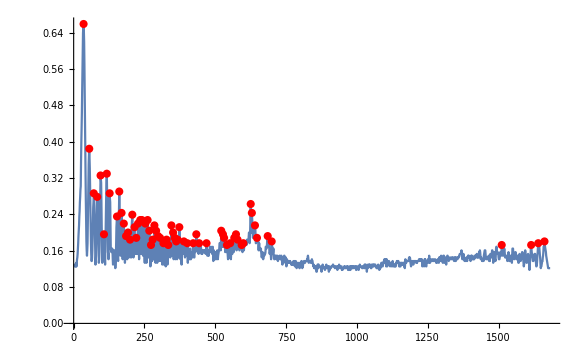

69

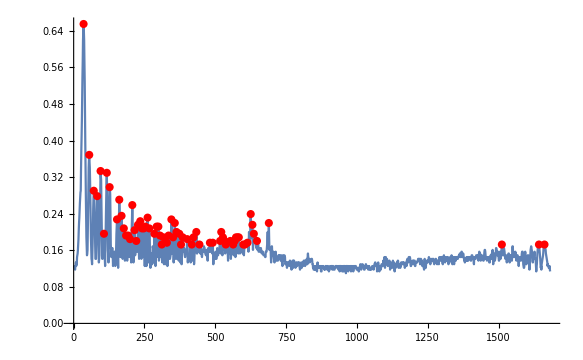

67

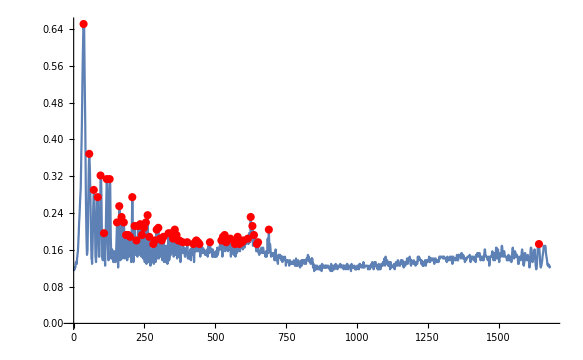

66

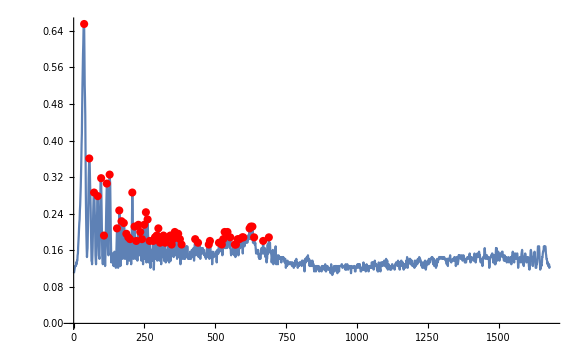

64

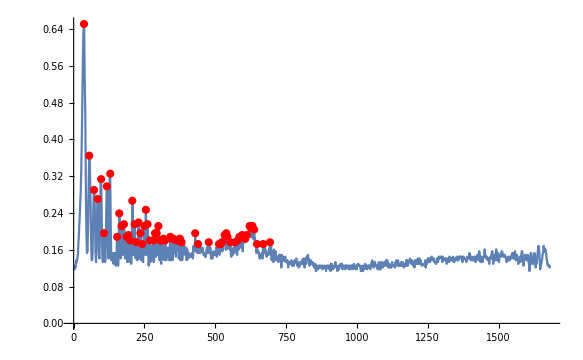

66

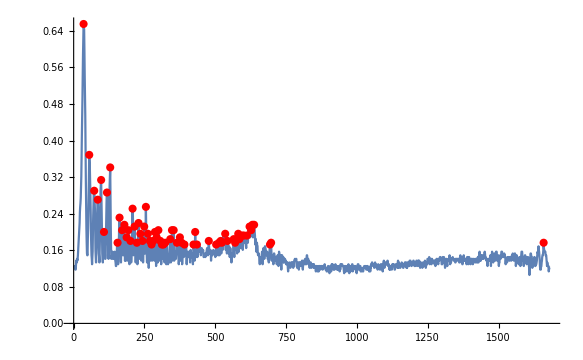

58

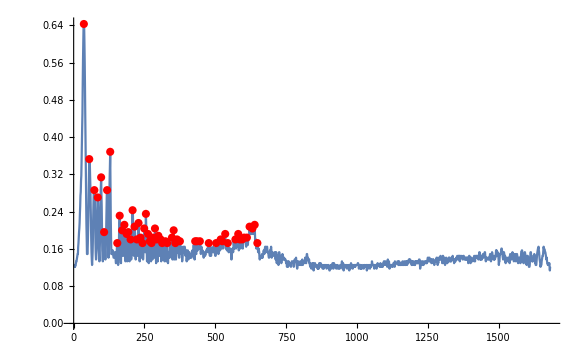

57

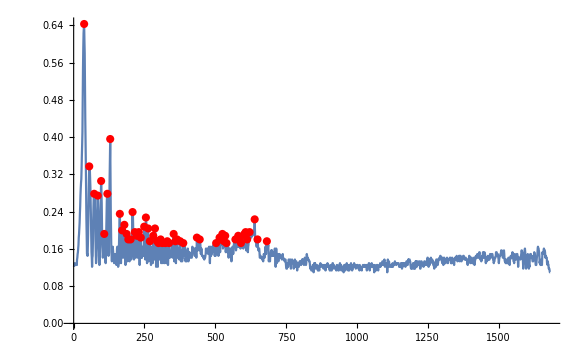

54

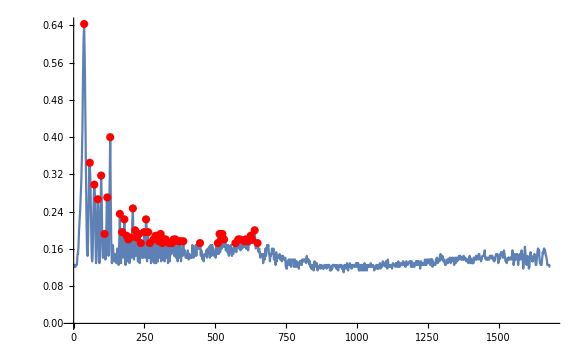

51

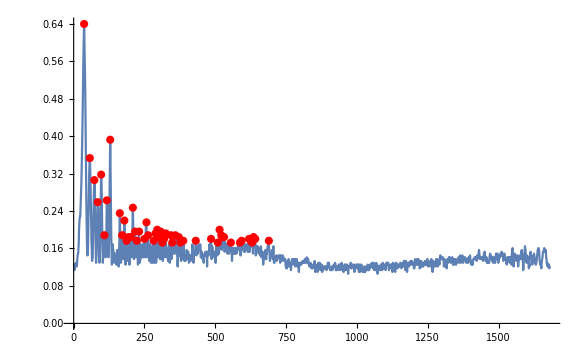

49

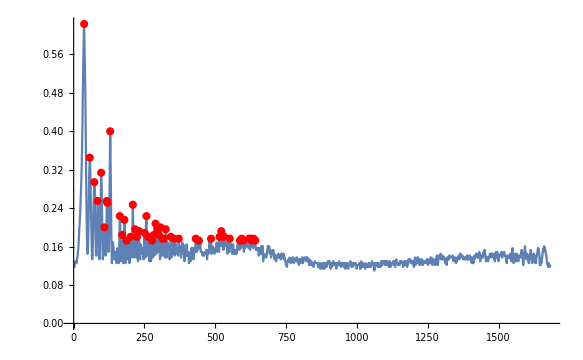

49

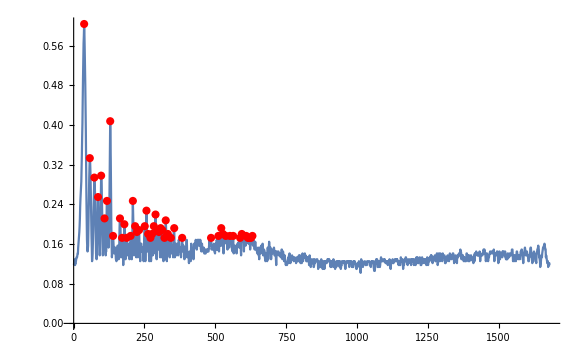

46

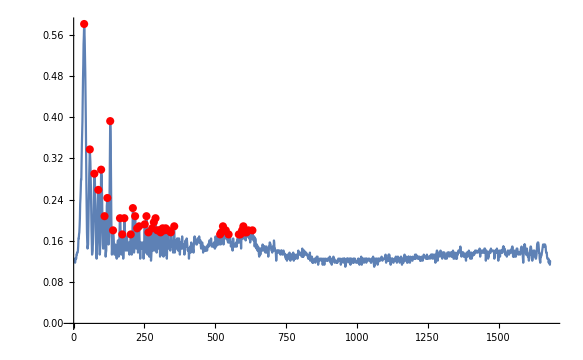

51

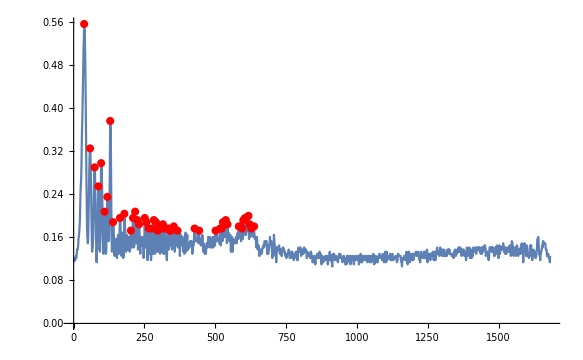

45

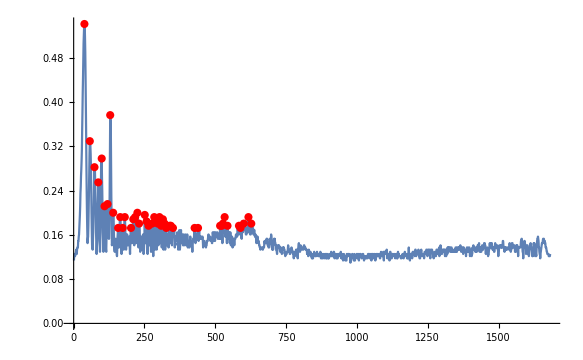

44

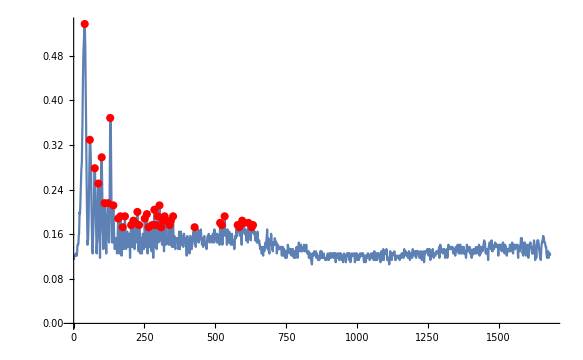

33

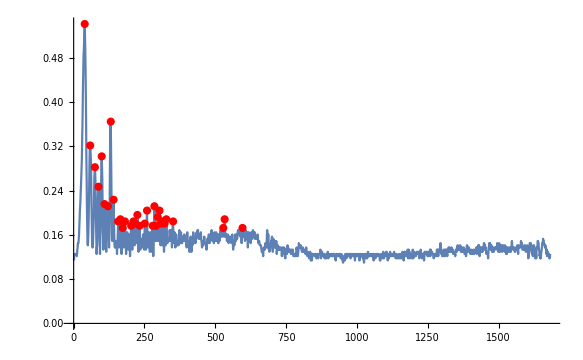

31

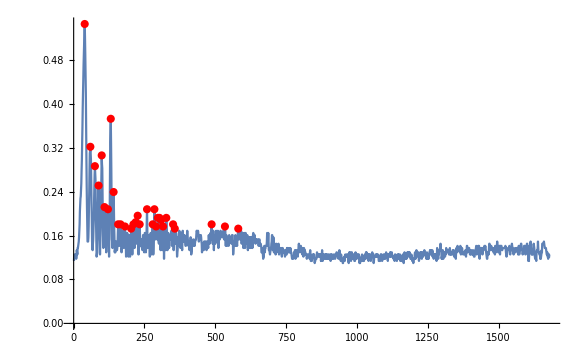

32

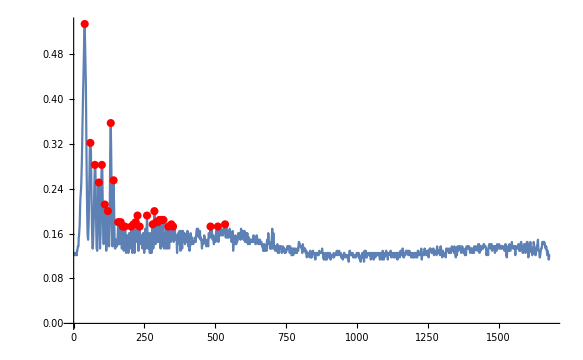

33

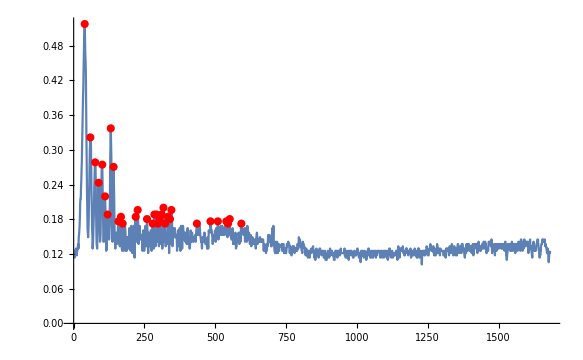

30

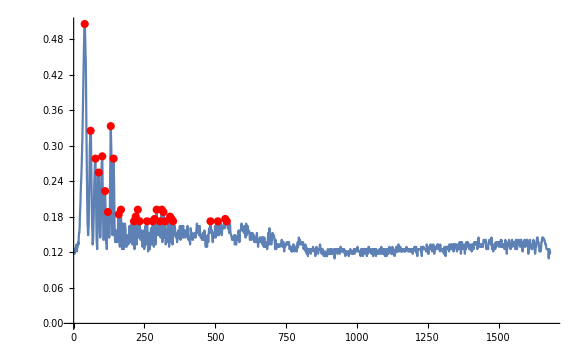

29

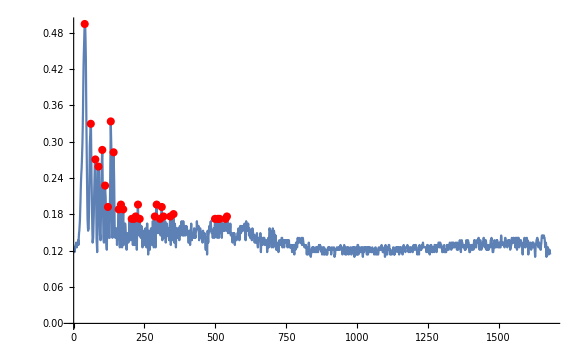

25

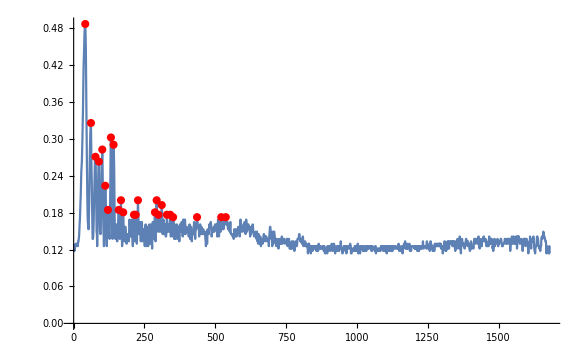

28

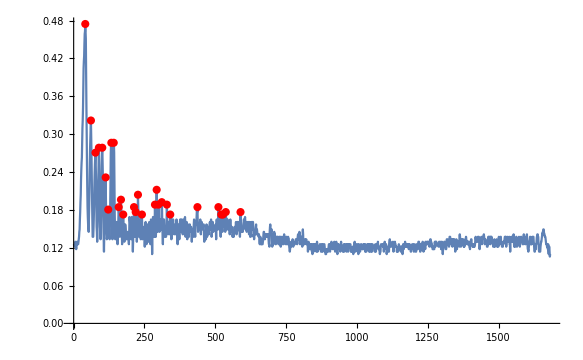

28

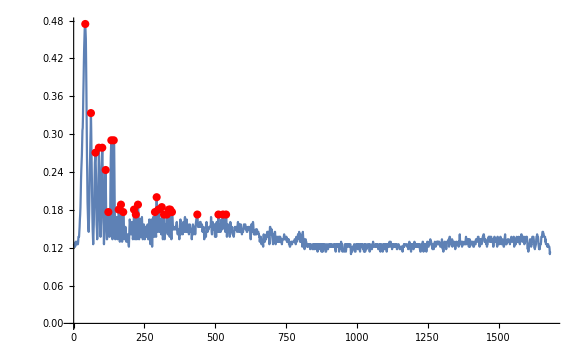

25

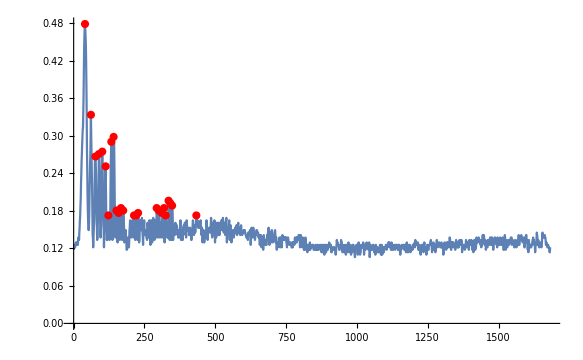

27

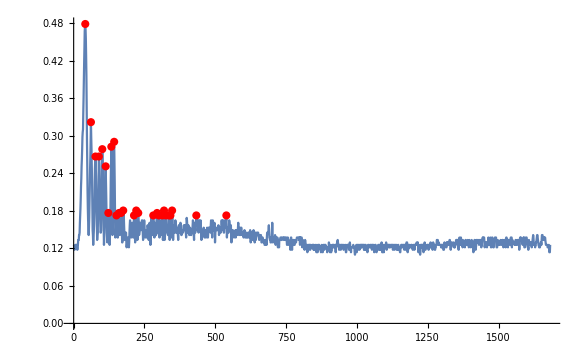

22

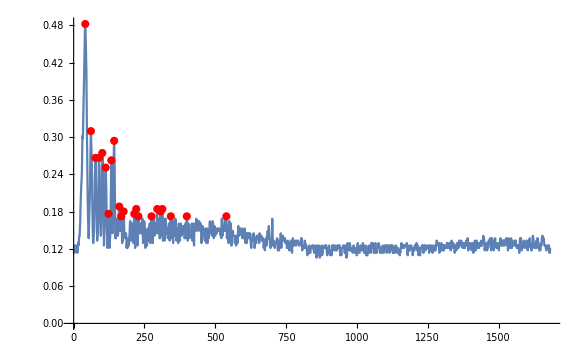

23

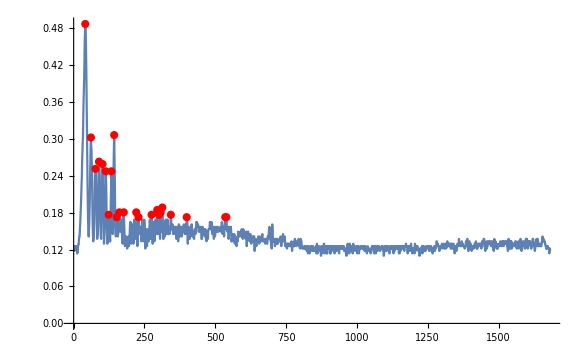

24

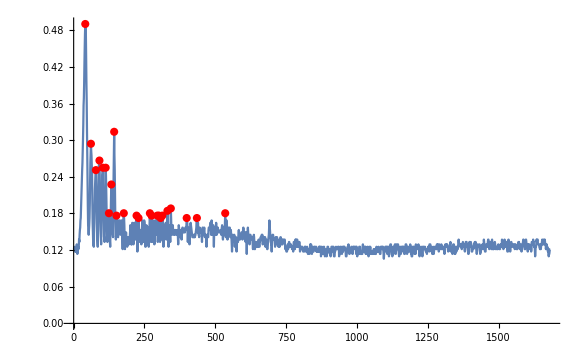

21

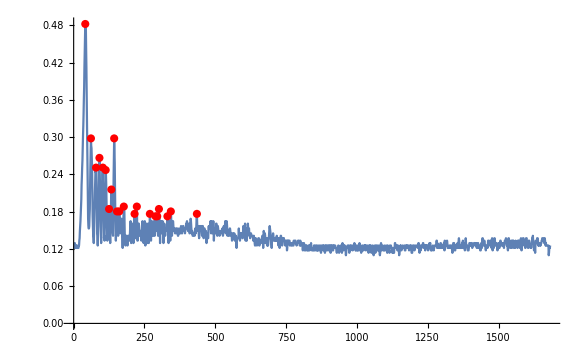

23

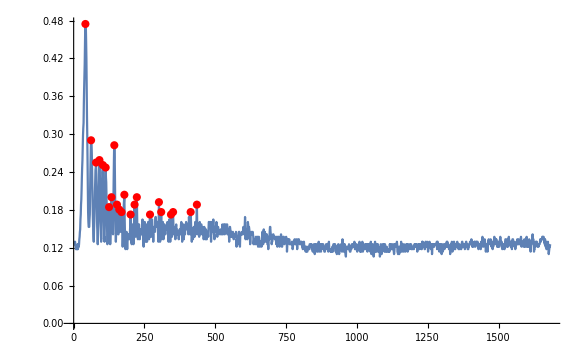

18

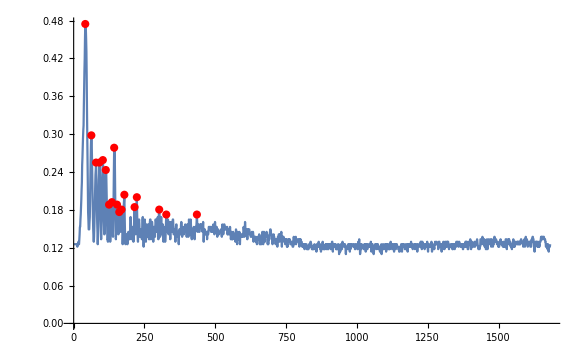

19

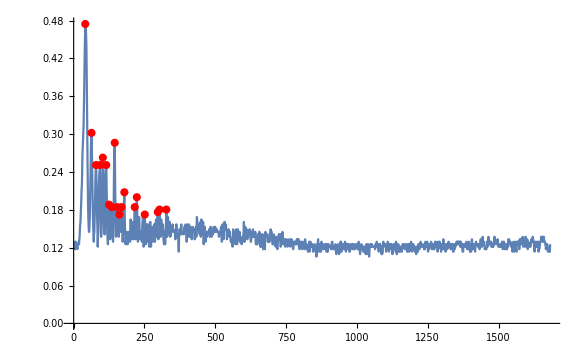

17

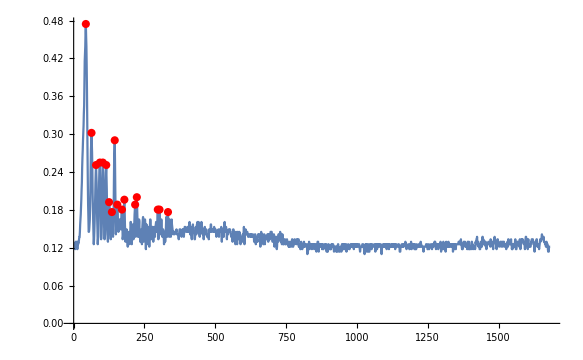

16

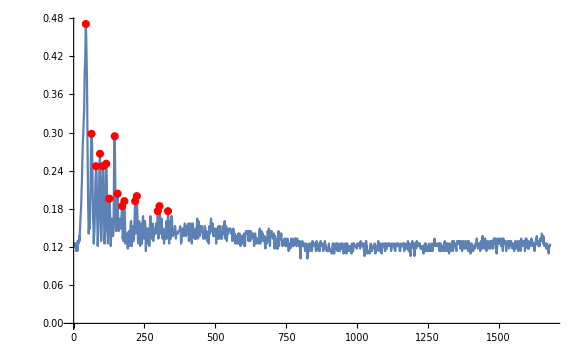

16

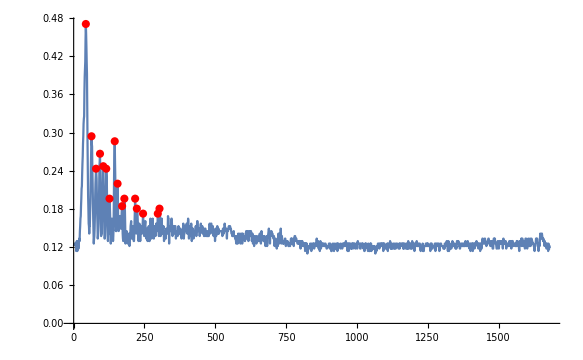

13

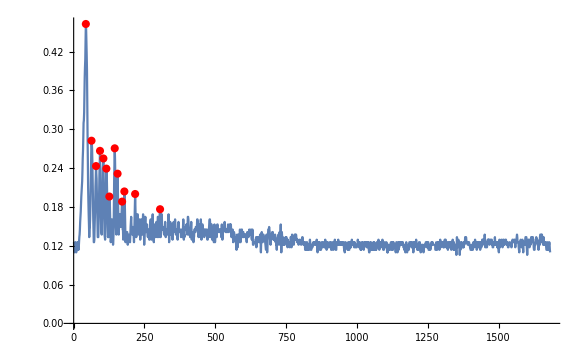

16

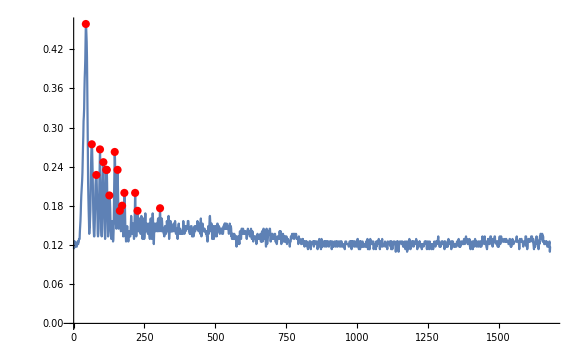

16

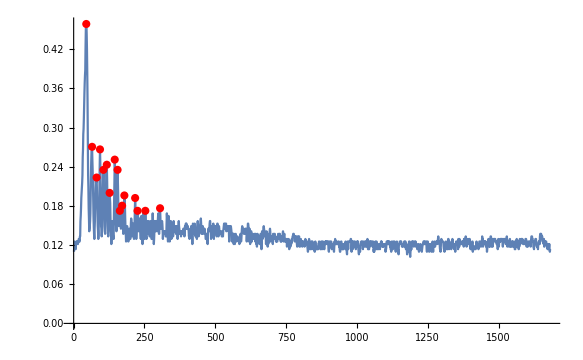

16

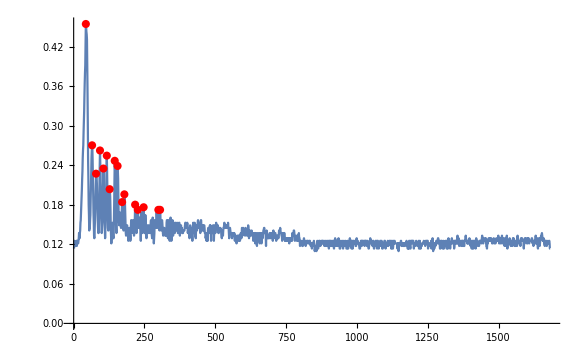

16

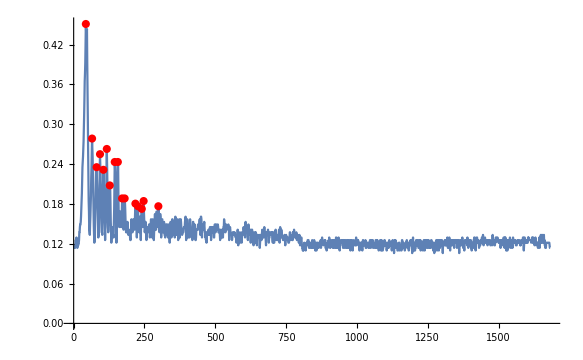

15

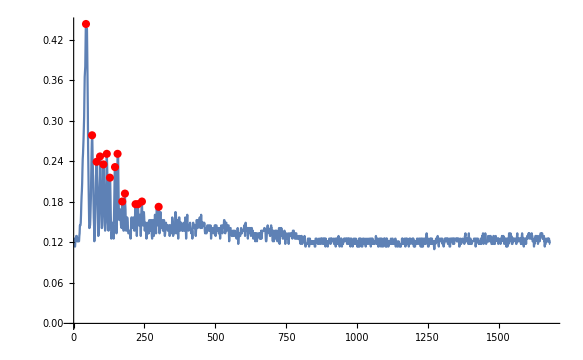

14

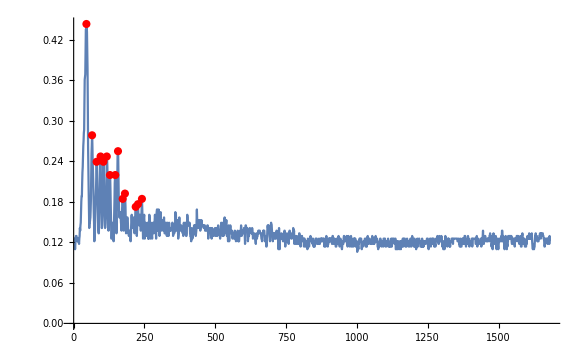

```mathematica
MyYRange=Range[600,710];
XMin=190;
XMax=-50;
For[i=MyYRange[[1]],i<MyYRange[[-1]],i++,
PicPic=MyPic[[i,XMin;;XMax,1]];
peaks=FindPeaks[MyPic[[i,XMin;;XMax,1]],1.7,0,0.17];
AppendTo[ListofLength,Length[peaks]];
Print[Length[peaks]];
Print[ListPlot[PicPic,Joined->True,PlotRange->All,Epilog->{Red,PointSize[0.01],Point[peaks]}]]];
```

```mathematica
ListofLength
```

{24,23,23,26,24,24,24,24,22,24,23,23,23,24,25,24,26,26,26,24,26,26,26,26,25,27,23,26,23,23,22,23,22,23,22,22,24,23,22,25,23,24,23,23,24,26,25,25,23,24,84,84,86,83,83,83,85,84,86,85,83,84,85,84,83,83,83,84,83,84,84,85,83,84,85,83,84,84,84,85,83,85,83,83,83,83,84,85,84,83,84,83,84,87,83,81,83,81,80,78,74,74,71,65,65,62,59,54,54,54,49,51,48,46,44,42,43,44,38,37,35,34,34,35,34,34,32,33,32,30,28,28,26,27,25,27,22,21,23,22,21,20,19,20,21,21,18,18,17,18,15,15,16,16,16,16,14,13,13,14,13,13,12,12,11,11,9,9,9,9,84,84,86,83,83,83,85,84,86,85,83,84,85,84,83,83,83,84,83,84,84,85,83,84,85,83,84,84,84,85,83,85,83,83,83,83,84,85,84,83,84,83,84,87,83,81,83,81,80,78,74,74,71,65,65,62,59,54,54,54,49,51,48,46,44,42,43,44,38,37,35,34,34,35,34,34,32,33,32,30,28,28,26,27,25,27,22,21,23,22,21,20,19,20,21,21,18,18,17,18,15,15,16,16,16,16,14,13,13,14,13,13,12,12,11,11,9,9,9,9,84,84,86,83,83,83,85,84,86,85,83,84,85,84,83,83,83,84,83,84,84,85,83,84,85,83,84,84,84,85,83,85,83,83,83,83,84,85,84,83,84,83,84,87,83,81,83,81,80,78,74,74,71,65,65,62,59,54,54,54,49,51,48,46,44,42,43,44,38,37,35,34,34,35,34,34,32,33,32,30,28,28,26,27,25,27,22,21,23,22,21,20,19,20,21,21,18,18,17,18,15,15,16,16,16,16,14,13,13,14,13,13,12,12,11,11,9,9,9,9,74,74,71,65,65,62,59,54,54,54,49,51,48,46,44,42,43,44,38,37,35,34,34,35,34,34,32,33,32,30,28,28,26,27,25,27,22,21,23,22,21,20,19,20,21,21,18,18,17,18,278,266,276,267,269,267,268,270,267,266,264,250,252,250,249,246,249,244,248,239,245,240,244,237,234,230,230,227,232,217,217,213,213,216,219,202,193,197,189,184,187,185,181,171,163,156,141,142,129,134,121,117,117,110,104,98,96,97,102,96,87,90,82,72,73,72,66,69,67,66,64,66,58,57,54,51,49,49,46,51,45,44,33,31,32,33,30,29,25,28,28,25,27,22,23,24,21,23,18,19,17,16,16,13,16,16,16,16,15,14}

PixelValue::imginv: Expecting an image or graphics instead of mypic.